```mathematica
data=Import[NotebookDirectory[]<>"/ising.txt","Table"];
```

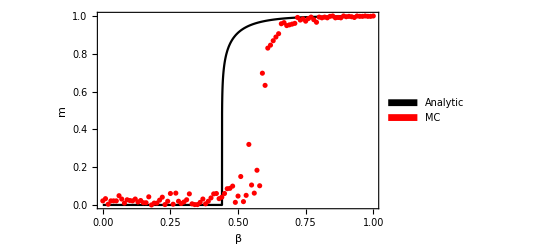

```mathematica
plot=Show[
Plot[(1-Max[1,Sinh[2β]]^-4)^(1/8),{β,0,1},Exclusions->None,PlotStyle->GrayLevel[0],
PlotLegends->SwatchLegend[{Black,Red},{"Analytic","MC"}],
Frame->True,FrameLabel->{"β","m"}],
ListPlot[data⟦3;;,;;⟧,PlotStyle->Red]];
Export[NotebookDirectory[]<>"/Ising.png",plot,ImageResolution->100];
plot
```